# Contact Angle : Mixed SAM with SPCE water - 2000

### Import Data

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*PathMD="/home/eixeres/Downloads/Berendsen/densmaps_s17_w3000/";*)
(*PathMD="/Users/burbol/Desktop/Testing/files_for_laila/densmaps_berendsen/densmaps_s17_w3000/";*)
PathMD="/Users/burbol/Downloads/g_rad_densmaps/";
input = Import[PathMD<>"g_rad_dmap_0pc_w5000_2.0ns_2.5ns.dat"];
Tinput=Transpose[input];
start = 0;
Length[input]
Length[Tinput]
```

1000

201

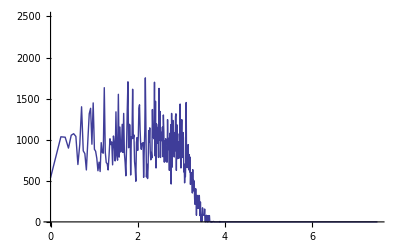

```mathematica
checkslice=85; (* Which slice to show *)
ListR=input[[All,{1,checkslice}]];
ListPlot[ListR,Joined->True,PlotRange->{0,2500}]
```

```mathematica
ListR
```

{{0.,536.916},{0.23717,1035.56},{0.33541,1030.78},{0.41079,898.05},{0.47434,1054.7},{0.53033,1073.22},{0.58095,1040.35},{0.6275,698.348},{0.67082,945.278},{0.71151,1400.87},{0.75,864.563},{0.78661,831.076},{0.82158,631.984},{0.85513,987.723},{0.88741,1315.37},{0.91856,1382.34},{0.94868,945.278},{0.97788,1448.1},{1.00623,883.698},{1.0338,859.779},{1.06066,774.279},{1.08685,622.416},{1.11243,727.051},{1.13743,612.848},{1.1619,964.414},{1.18585,845.427},{1.20934,835.859},{1.23238,1633.45},{1.25499,850.211},{1.2772,722.267},{1.29904,707.915},{1.32051,631.984},{1.34164,807.766},{1.36244,1011.64},{1.38293,940.494},{1.40312,973.982},{1.42302,694.174},{1.44265,1045.13},{1.46202,959.02},{1.48113,741.402},{1.5,1339.29},{1.51863,807.766},{1.53704,750.97},{1.55523,1552.73},{1.57321,788.631},{1.59099,1153.94},{1.60857,850.211},{1.62596,888.482},{1.64317,1187.43},{1.6602,845.427},{1.67705,1320.15},{1.69374,831.686},{1.71026,722.267},{1.72663,560.836},{1.74284,907.618},{1.75891,1358.42},{1.77482,1704.6},{1.7906,902.223},{1.80624,1187.43},{1.82174,1177.86},{1.83712,570.403},{1.85236,1035.56},{1.86748,1011.64},{1.88249,1614.31},{1.89737,1016.43},{1.91213,1058.87},{1.92678,731.835},{1.94133,646.335},{1.95576,494.472},{1.97009,969.198},{1.98431,1025.99},{1.99844,869.347},{2.01246,1044.52},{2.02639,1381.73},{2.04022,1424.79},{2.05396,1116.28},{2.06761,940.494},{2.08117,883.698},{2.09464,954.846},{2.10802,930.927},{2.12132,964.414},{2.13454,541.7},{2.14767,854.995},{2.16073,1106.71},{2.17371,1752.43},{2.18661,1173.07},{2.19943,546.484},{2.21218,703.131},{2.22486,527.349},{2.23747,665.471},{2.25,1111.49},{2.26247,969.198},{2.27486,1144.37},{2.28719,841.254},{2.29946,755.144},{2.31166,845.427},{2.32379,779.063},{2.33586,1367.38},{2.34787,1045.13},{2.35982,1025.99},{2.37171,1011.64},{2.38354,1699.81},{2.39531,802.983},{2.40702,1467.23},{2.41868,655.903},{2.43028,1192.21},{2.44182,1140.2},{2.45331,959.63},{2.46475,1139.59},{2.47614,783.847},{2.48747,1624.49},{2.49875,992.507},{2.50998,1344.07},{2.52116,783.847},{2.53229,1092.36},{2.54337,1002.07},{2.55441,987.723},{2.56539,1153.94},{2.57633,793.415},{2.58723,1301.02},{2.59808,1092.36},{2.60888,727.051},{2.61964,988.333},{2.63035,916.575},{2.64102,1011.64},{2.65165,731.835},{2.66224,878.914},{2.67278,727.051},{2.68328,1244.22},{2.69374,878.914},{2.70416,1016.43},{2.71454,926.143},{2.72489,627.2},{2.73519,1078.01},{2.74545,878.914},{2.75568,1182.64},{2.76586,460.985},{2.77601,1320.15},{2.78613,665.471},{2.7962,926.143},{2.80624,1234.65},{2.81625,893.266},{2.82622,954.846},{2.83615,789.241},{2.84605,1087.57},{2.85591,864.563},{2.86575,1282.49},{2.87554,1315.37},{2.88531,627.2},{2.89504,1182.64},{2.90474,950.062},{2.9144,769.495},{2.92404,798.199},{2.93364,973.371},{2.94321,774.279},{2.95275,1073.22},{2.96226,945.278},{2.97174,1434.36},{2.98119,945.889},{2.99061,655.903},{3.,1044.52},{3.00936,1244.22},{3.01869,840.643},{3.02799,783.847},{3.03727,1087.57},{3.04651,1025.99},{3.05573,608.064},{3.06492,703.131},{3.07409,475.336},{3.08322,608.064},{3.09233,551.268},{3.10141,731.224},{3.11047,1452.88},{3.1195,664.86},{3.1285,683.996},{3.13748,916.575},{3.14643,660.077},{3.15535,940.494},{3.16425,740.792},{3.17313,631.984},{3.18198,816.724},{3.19081,608.064},{3.19961,788.631},{3.20839,456.201},{3.21714,603.28},{3.22587,517.781},{3.23458,593.713},{3.24326,517.781},{3.25192,351.566},{3.26056,636.157},{3.26917,375.485},{3.27777,503.429},{3.28634,503.429},{3.29488,489.078},{3.30341,285.202},{3.31191,214.054},{3.32039,270.85},{3.32885,403.578},{3.33729,261.282},{3.34571,80.7156},{3.3541,251.715},{3.36248,322.862},{3.37083,166.215},{3.37916,170.999},{3.38748,242.147},{3.39577,166.215},{3.40404,322.862},{3.41229,313.295},{3.42053,185.351},{3.42874,75.9317},{3.43693,242.147},{3.44511,95.0673},{3.45326,4.78388},{3.46139,80.7156},{3.46951,4.78388},{3.47761,75.9317},{3.48569,170.999},{3.49374,90.2834},{3.50179,80.7156},{3.50981,80.7156},{3.51781,80.7156},{3.5258,85.4995},{3.53377,156.647},{3.54172,9.56776},{3.54965,0.},{3.55756,14.3516},{3.56546,4.78388},{3.57334,80.7156},{3.5812,9.56776},{3.58905,0.},{3.59687,4.78388},{3.60468,75.9317},{3.61248,0.},{3.62026,4.78388},{3.62802,75.9317},{3.63576,75.9317},{3.64349,75.9317},{3.6512,9.56776},{3.65889,0.},{3.66657,0.},{3.67423,0.},{3.68188,0.},{3.68951,0.},{3.69713,4.78388},{3.70473,0.},{3.71231,0.},{3.71988,0.},{3.72743,4.78388},{3.73497,4.78388},{3.74249,4.78388},{3.75,0.},{3.75749,0.},{3.76497,0.},{3.77243,0.},{3.77988,0.},{3.78731,0.},{3.79473,0.},{3.80214,0.},{3.80953,0.},{3.8169,0.},{3.82426,0.},{3.83161,0.},{3.83895,0.},{3.84626,0.},{3.85357,0.},{3.86086,0.},{3.86814,0.},{3.8754,0.},{3.88265,4.78388},{3.88989,0.},{3.89711,0.},{3.90432,0.},{3.91152,0.},{3.91871,0.},{3.92588,0.},{3.93303,0.},{3.94018,0.},{3.94731,0.},{3.95443,0.},{3.96153,0.},{3.96863,0.},{3.97571,0.},{3.98278,0.},{3.98983,0.},{3.99687,0.},{4.0039,0.},{4.01092,0.},{4.01793,0.},{4.02492,0.},{4.0319,0.},{4.03887,0.},{4.04583,0.},{4.05278,0.},{4.05971,0.},{4.06663,0.},{4.07354,0.},{4.08044,0.},{4.08733,0.},{4.0942,0.},{4.10107,0.},{4.10792,0.},{4.11476,0.},{4.12159,0.},{4.12841,0.},{4.13521,0.},{4.14201,0.},{4.1488,0.},{4.15557,0.},{4.16233,0.},{4.16908,0.},{4.17582,0.},{4.18255,0.},{4.18927,0.},{4.19598,0.},{4.20268,0.},{4.20936,0.},{4.21604,0.},{4.22271,0.},{4.22936,0.},{4.23601,0.},{4.24264,0.},{4.24926,0.},{4.25588,0.},{4.26248,0.},{4.26907,0.},{4.27566,0.},{4.28223,0.},{4.28879,0.},{4.29535,0.},{4.30189,0.},{4.30842,0.},{4.31494,0.},{4.32146,0.},{4.32796,0.},{4.33445,0.},{4.34094,0.},{4.34741,0.},{4.35388,0.},{4.36033,0.},{4.36678,0.},{4.37321,0.},{4.37964,0.},{4.38606,0.},{4.39247,0.},{4.39886,0.},{4.40525,0.},{4.41163,0.},{4.418,0.},{4.42436,0.},{4.43072,0.},{4.43706,0.},{4.44339,0.},{4.44972,0.},{4.45604,0.},{4.46234,0.},{4.46864,0.},{4.47493,0.},{4.48121,0.},{4.48748,0.},{4.49375,0.},{4.5,0.},{4.50625,0.},{4.51248,0.},{4.51871,0.},{4.52493,0.},{4.53114,0.},{4.53735,0.},{4.54354,0.},{4.54973,0.},{4.5559,0.},{4.56207,0.},{4.56823,0.},{4.57439,0.},{4.58053,0.},{4.58667,0.},{4.59279,0.},{4.59891,0.},{4.60502,0.},{4.61113,0.},{4.61722,0.},{4.62331,0.},{4.62939,0.},{4.63546,0.},{4.64152,0.},{4.64758,0.},{4.65363,0.},{4.65967,0.},{4.6657,0.},{4.67172,0.},{4.67774,0.},{4.68375,0.},{4.68975,0.},{4.69574,0.},{4.70173,0.},{4.70771,0.},{4.71368,0.},{4.71964,0.},{4.7256,0.},{4.73154,0.},{4.73748,0.},{4.74342,0.},{4.74934,0.},{4.75526,0.},{4.76117,0.},{4.76707,0.},{4.77297,0.},{4.77886,0.},{4.78474,0.},{4.79062,0.},{4.79648,0.},{4.80234,0.},{4.8082,0.},{4.81404,0.},{4.81988,0.},{4.82571,0.},{4.83154,0.},{4.83735,0.},{4.84317,0.},{4.84897,0.},{4.85477,0.},{4.86056,0.},{4.86634,0.},{4.87211,0.},{4.87788,0.},{4.88365,0.},{4.8894,0.},{4.89515,0.},{4.90089,0.},{4.90663,0.},{4.91236,0.},{4.91808,0.},{4.92379,0.},{4.9295,0.},{4.93521,0.},{4.9409,0.},{4.94659,0.},{4.95227,0.},{4.95795,0.},{4.96362,0.},{4.96928,0.},{4.97494,0.},{4.98059,0.},{4.98623,0.},{4.99187,0.},{4.9975,0.},{5.00312,0.},{5.00874,0.},{5.01435,0.},{5.01996,0.},{5.02556,0.},{5.03115,0.},{5.03674,0.},{5.04232,0.},{5.0479,0.},{5.05346,0.},{5.05903,0.},{5.06458,0.},{5.07013,0.},{5.07568,0.},{5.08122,0.},{5.08675,0.},{5.09227,0.},{5.09779,0.},{5.10331,0.},{5.10882,0.},{5.11432,0.},{5.11981,0.},{5.1253,0.},{5.13079,0.},{5.13627,0.},{5.14174,0.},{5.14721,0.},{5.15267,0.},{5.15812,0.},{5.16357,0.},{5.16902,0.},{5.17446,0.},{5.17989,0.},{5.18532,0.},{5.19074,0.},{5.19615,0.},{5.20156,0.},{5.20697,0.},{5.21237,0.},{5.21776,0.},{5.22315,0.},{5.22853,0.},{5.2339,0.},{5.23927,0.},{5.24464,0.},{5.25,0.},{5.25535,0.},{5.2607,0.},{5.26605,0.},{5.27139,0.},{5.27672,0.},{5.28205,0.},{5.28737,0.},{5.29268,0.},{5.29799,0.},{5.3033,0.},{5.3086,0.},{5.3139,0.},{5.31919,0.},{5.32447,0.},{5.32975,0.},{5.33503,0.},{5.34029,0.},{5.34556,0.},{5.35082,0.},{5.35607,0.},{5.36132,0.},{5.36656,0.},{5.3718,0.},{5.37703,0.},{5.38226,0.},{5.38749,0.},{5.3927,0.},{5.39792,0.},{5.40312,0.},{5.40833,0.},{5.41352,0.},{5.41872,0.},{5.42391,0.},{5.42909,0.},{5.43427,0.},{5.43944,0.},{5.44461,0.},{5.44977,0.},{5.45493,0.},{5.46008,0.},{5.46523,0.},{5.47037,0.},{5.47551,0.},{5.48065,0.},{5.48578,0.},{5.4909,0.},{5.49602,0.},{5.50114,0.},{5.50625,0.},{5.51135,0.},{5.51645,0.},{5.52155,0.},{5.52664,0.},{5.53173,0.},{5.53681,0.},{5.54189,0.},{5.54696,0.},{5.55203,0.},{5.55709,0.},{5.56215,0.},{5.5672,0.},{5.57225,0.},{5.5773,0.},{5.58234,0.},{5.58737,0.},{5.59241,0.},{5.59743,0.},{5.60245,0.},{5.60747,0.},{5.61249,0.},{5.61749,0.},{5.6225,0.},{5.6275,0.},{5.6325,0.},{5.63749,0.},{5.64247,0.},{5.64746,0.},{5.65243,0.},{5.65741,0.},{5.66238,0.},{5.66734,0.},{5.6723,0.},{5.67726,0.},{5.68221,0.},{5.68716,0.},{5.6921,0.},{5.69704,0.},{5.70197,0.},{5.7069,0.},{5.71183,0.},{5.71675,0.},{5.72167,0.},{5.72658,0.},{5.73149,0.},{5.7364,0.},{5.7413,0.},{5.74619,0.},{5.75109,0.},{5.75598,0.},{5.76086,0.},{5.76574,0.},{5.77062,0.},{5.77549,0.},{5.78035,0.},{5.78522,0.},{5.79008,0.},{5.79493,0.},{5.79978,0.},{5.80463,0.},{5.80948,0.},{5.81431,0.},{5.81915,0.},{5.82398,0.},{5.82881,0.},{5.83363,0.},{5.83845,0.},{5.84327,0.},{5.84808,0.},{5.85288,0.},{5.85769,0.},{5.86249,0.},{5.86728,0.},{5.87207,0.},{5.87686,0.},{5.88165,0.},{5.88643,0.},{5.8912,0.},{5.89597,0.},{5.90074,0.},{5.90551,0.},{5.91027,0.},{5.91502,0.},{5.91978,0.},{5.92453,0.},{5.92927,0.},{5.93401,0.},{5.93875,0.},{5.94348,0.},{5.94821,0.},{5.95294,0.},{5.95766,0.},{5.96238,0.},{5.9671,0.},{5.97181,0.},{5.97652,0.},{5.98122,0.},{5.98592,0.},{5.99062,0.},{5.99531,0.},{6.,0.},{6.00469,0.},{6.00937,0.},{6.01405,0.},{6.01872,0.},{6.02339,0.},{6.02806,0.},{6.03272,0.},{6.03738,0.},{6.04204,0.},{6.04669,0.},{6.05134,0.},{6.05599,0.},{6.06063,0.},{6.06527,0.},{6.06991,0.},{6.07454,0.},{6.07917,0.},{6.08379,0.},{6.08841,0.},{6.09303,0.},{6.09764,0.},{6.10225,0.},{6.10686,0.},{6.11146,0.},{6.11606,0.},{6.12066,0.},{6.12526,0.},{6.12985,0.},{6.13443,0.},{6.13901,0.},{6.14359,0.},{6.14817,0.},{6.15274,0.},{6.15731,0.},{6.16188,0.},{6.16644,0.},{6.171,0.},{6.17556,0.},{6.18011,0.},{6.18466,0.},{6.1892,0.},{6.19375,0.},{6.19829,0.},{6.20282,0.},{6.20735,0.},{6.21188,0.},{6.21641,0.},{6.22093,0.},{6.22545,0.},{6.22997,0.},{6.23448,0.},{6.23899,0.},{6.2435,0.},{6.248,0.},{6.2525,0.},{6.257,0.},{6.26149,0.},{6.26598,0.},{6.27047,0.},{6.27495,0.},{6.27943,0.},{6.28391,0.},{6.28838,0.},{6.29285,0.},{6.29732,0.},{6.30179,0.},{6.30625,0.},{6.31071,0.},{6.31516,0.},{6.31961,0.},{6.32406,0.},{6.32851,0.},{6.33295,0.},{6.33739,0.},{6.34183,0.},{6.34626,0.},{6.35069,0.},{6.35512,0.},{6.35954,0.},{6.36396,0.},{6.36838,0.},{6.37279,0.},{6.37721,0.},{6.38161,0.},{6.38602,0.},{6.39042,0.},{6.39482,0.},{6.39922,0.},{6.40361,0.},{6.408,0.},{6.41239,0.},{6.41677,0.},{6.42116,0.},{6.42553,0.},{6.42991,0.},{6.43428,0.},{6.43865,0.},{6.44302,0.},{6.44738,0.},{6.45174,0.},{6.4561,0.},{6.46046,0.},{6.46481,0.},{6.46916,0.},{6.4735,0.},{6.47785,0.},{6.48219,0.},{6.48652,0.},{6.49086,0.},{6.49519,0.},{6.49952,0.},{6.50385,0.},{6.50817,0.},{6.51249,0.},{6.51681,0.},{6.52112,0.},{6.52543,0.},{6.52974,0.},{6.53405,0.},{6.53835,0.},{6.54265,0.},{6.54695,0.},{6.55124,0.},{6.55553,0.},{6.55982,0.},{6.56411,0.},{6.56839,0.},{6.57267,0.},{6.57695,0.},{6.58122,0.},{6.5855,0.},{6.58976,0.},{6.59403,0.},{6.5983,0.},{6.60256,0.},{6.60681,0.},{6.61107,0.},{6.61532,0.},{6.61957,0.},{6.62382,0.},{6.62807,0.},{6.63231,0.},{6.63655,0.},{6.64078,0.},{6.64502,0.},{6.64925,0.},{6.65348,0.},{6.6577,0.},{6.66193,0.},{6.66615,0.},{6.67036,0.},{6.67458,0.},{6.67879,0.},{6.683,0.},{6.68721,0.},{6.69141,0.},{6.69561,0.},{6.69981,0.},{6.70401,0.},{6.7082,0.},{6.7124,0.},{6.71658,0.},{6.72077,0.},{6.72495,0.},{6.72913,0.},{6.73331,0.},{6.73749,0.},{6.74166,0.},{6.74583,0.},{6.75,0.},{6.75417,0.},{6.75833,0.},{6.76249,0.},{6.76665,0.},{6.7708,0.},{6.77495,0.},{6.7791,0.},{6.78325,0.},{6.7874,0.},{6.79154,0.},{6.79568,0.},{6.79982,0.},{6.80395,0.},{6.80808,0.},{6.81221,0.},{6.81634,0.},{6.82047,0.},{6.82459,0.},{6.82871,0.},{6.83283,0.},{6.83694,0.},{6.84105,0.},{6.84516,0.},{6.84927,0.},{6.85338,0.},{6.85748,0.},{6.86158,0.},{6.86568,0.},{6.86977,0.},{6.87386,0.},{6.87795,0.},{6.88204,0.},{6.88613,0.},{6.89021,0.},{6.89429,0.},{6.89837,0.},{6.90245,0.},{6.90652,0.},{6.91059,0.},{6.91466,0.},{6.91872,0.},{6.92279,0.},{6.92685,0.},{6.93091,0.},{6.93497,0.},{6.93902,0.},{6.94307,0.},{6.94712,0.},{6.95117,0.},{6.95521,0.},{6.95926,0.},{6.9633,0.},{6.96733,0.},{6.97137,0.},{6.9754,0.},{6.97943,0.},{6.98346,0.},{6.98749,0.},{6.99151,0.},{6.99553,0.},{6.99955,0.},{7.00357,0.},{7.00759,0.},{7.0116,0.},{7.01561,0.},{7.01962,0.},{7.02362,0.},{7.02762,0.},{7.03162,0.},{7.03562,0.},{7.03962,0.},{7.04361,0.},{7.04761,0.},{7.0516,0.},{7.05558,0.},{7.05957,0.},{7.06355,0.},{7.06753,0.},{7.07151,0.},{7.07549,0.},{7.07946,0.},{7.08343,0.},{7.0874,0.},{7.09137,0.},{7.09533,0.},{7.0993,0.},{7.10326,0.},{7.10721,0.},{7.11117,0.},{7.11512,0.},{7.11908,0.},{7.12303,0.},{7.12697,0.},{7.13092,0.},{7.13486,0.},{7.1388,0.},{7.14274,0.},{7.14668,0.},{7.15061,0.},{7.15454,0.},{7.15847,0.},{7.1624,0.},{7.16633,0.},{7.17025,0.},{7.17417,0.},{7.17809,0.},{7.18201,0.},{7.18592,0.},{7.18984,0.},{7.19375,0.},{7.19766,0.},{7.20156,0.},{7.20547,0.},{7.20937,0.},{7.21327,0.},{7.21717,0.},{7.22106,0.},{7.22496,0.},{7.22885,0.},{7.23274,0.},{7.23663,0.},{7.24051,0.},{7.24439,0.},{7.24828,0.},{7.25215,0.},{7.25603,0.},{7.25991,0.},{7.26378,0.},{7.26765,0.},{7.27152,0.},{7.27539,0.},{7.27925,0.},{7.28311,0.},{7.28697,0.},{7.29083,0.},{7.29469,0.},{7.29854,0.},{7.3024,0.},{7.30625,0.},{7.3101,0.},{7.31394,0.},{7.31779,0.},{7.32163,0.},{7.32547,0.},{7.32931,0.},{7.33314,0.},{7.33698,0.},{7.34081,0.},{7.34464,0.},{7.34847,0.},{7.3523,0.},{7.35612,0.},{7.35994,0.},{7.36376,0.},{7.36758,0.},{7.3714,0.},{7.37521,0.},{7.37902,0.},{7.38283,0.},{7.38664,0.},{7.39045,0.},{7.39425,0.},{7.39806,0.},{7.40186,0.},{7.40566,0.},{7.40945,0.},{7.41325,0.},{7.41704,0.},{7.42083,0.},{7.42462,0.},{7.42841,0.},{7.43219,0.},{7.43598,0.},{7.43976,0.},{7.44354,0.},{7.44731,0.},{7.45109,0.},{7.45486,0.},{7.45864,0.},{7.46241,0.},{7.46617,0.},{7.46994,0.},{7.4737,0.},{7.47747,0.},{7.48123,0.},{7.48498,0.},{7.48874,0.},{7.4925,0.},{7.49625,0.}}

### Sanity Check

{ρ→97.7774,R→3.15772,d→0.424739}

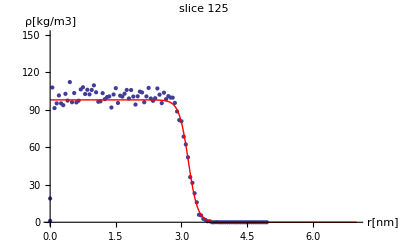

```mathematica
checkslice =125;
fitdata=Tinput[[All,{1,checkslice}]];
dslice=fitdata[[3,1]]-fitdata[[2,1]];
shift=-4.85;
plotdata = ListPlot[fitdata,PlotRange-> {{0,7},{0,150}}];
fitparam=FindFit[fitdata,ρ/2(1-Tanh[2*(r-R)/d]),{{ρ,100},{R,3},{d,1}},r]
plotfit = Plot[ρ/2(1-Tanh[2*(r-R)/d])/.fitparam,{r,0,7},PlotRange-> {{0,5},{0,150}},PlotStyle->Red];
Show[plotdata,plotfit,AxesLabel->{"r[nm]","ρ[kg/m3]"},PlotLabel->"slice "<>ToString[checkslice]]
```

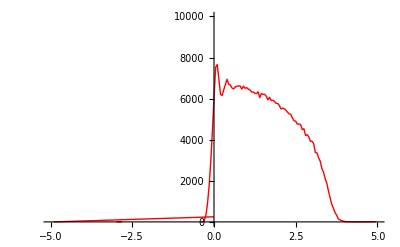

```mathematica
dens=Total[Tinput];
x=Tinput[[1]];
densdata=Thread[{x,dens}];
ListPlot[densdata,PlotRange-> {{-5,5},{0,10000}},Joined->True,PlotStyle->{Red,Thick}]
```

```mathematica
Position[densdata,Max[densdata]]
```

{{104,2}}

```mathematica
Max[densdata]
```

7662.

```mathematica
densdata[[104]]
```

{0.0999999,7662.}

### Determining the equimolar dividing planes

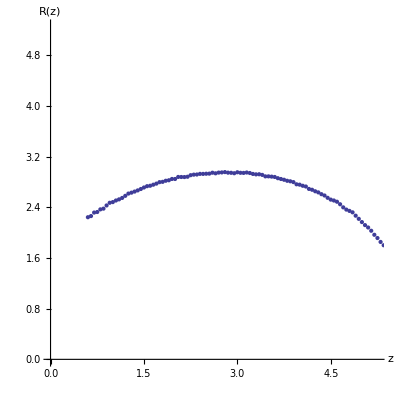

```mathematica
slicemin=81+16; (*Choose slices to plot*)
slicemax=198;

fitdata=Tinput[[All,{1,slicemin}]];
dslice=fitdata[[3,1]]-fitdata[[2,1]];
shift=input[[2,1]]+dslice +0.7;

radius=Table[{0,0},{i,1,slicemax-slicemin+1}];
Do[n=slicemin+(i-1);
fitdata=Tinput[[All,{1,n}]];
fitparam=FindFit[fitdata,ρ/2(1-Tanh[2*(r-R)/d]),{{ρ,100},{R,3},{d,1}},r];
radius[[i,1]]=n dslice+shift;radius[[i,2]]=R/.fitparam,{i,1,slicemax-slicemin+1}]
plotradius=ListPlot[radius,AxesLabel->{"z","R(z)"},PlotRange-> {{0,-shift+1},{0,-shift+1}},AspectRatio-> 1]
```

```mathematica
3
```

### Fitting a circle to the data

{R→3.03659,m→2.86251}

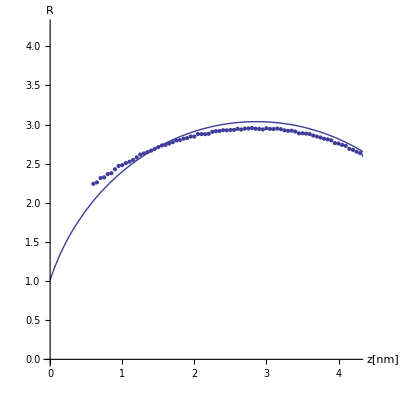

```mathematica
plotradius=ListPlot[radius,PlotRange-> {{0,-shift},{0,-shift}},AspectRatio-> 1];
fitcircle=FindFit[radius,Sqrt[R^2-(z-m)^2],{{R,3.1},{m,2.9}},z]  (*Choose some R and some m to start the start the approximation*)
fitcircleplot = Plot[Sqrt[R^2-(z-m)^2]/.fitcircle,{z,0,(R+m)/.fitcircle},PlotRange-> {{0,-shift},{0,-shift}},AspectRatio-> 1];
Show[plotradius,fitcircleplot,AxesLabel->{"z[nm]","R"}]
```

### Contact Angle

```mathematica
Subscript[Θ, c] = 90+180/π ArcTan[m/Sqrt[R^2-m^2]]/.fitcircle
Subscript[r, 0,c]= Sqrt[R^2-m^2]/.fitcircle
```

160.506

1.01335

### Fitting an ellipsoid to the data

{a→2.67981,b→2.95002,m→1.928}

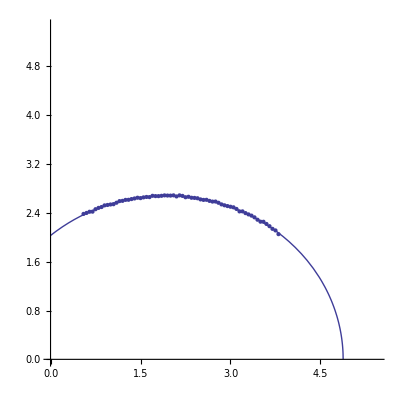

```mathematica
fitellipsoid=FindFit[radius,a*Sqrt[1-(z-m)^2/b^2],{{a,3.0},{b,3.0},{m,1.3}},z]
fitellipsoidplot = Plot[a*Sqrt[1-(z-m)^2/b^2]/.fitellipsoid,{z,0,(b+m)/.fitellipsoid},PlotRange-> {{0,4},{0,6}},AspectRatio-> 1];
Show[plotradius,fitellipsoidplot]
```

### Contact Angle

```mathematica
Subscript[Θ, e] = 90+180/π ArcTan[m*a/(b*Sqrt[b^2-m^2])]/.fitellipsoid
Subscript[r, 0,e]=a* Sqrt[1-(m/b)^2]/.fitellipsoid
```

ReplaceAll::reps: {fitellipsoid} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

90+(180 ArcTan[(a m)/(b √(b^2-m^2))])/π/.fitellipsoid

ReplaceAll::reps: {fitellipsoid} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a √(1-m^2/b^2)/.fitellipsoid

{{1,129.633},{3,130.8},{5,102.754},{7,140.292},{9,139.963},{11,144.127},{13,141.048},{15,135.476},{17,135.191},{19,137.569}}

{a→143.623,b→-21.4749,c→11.0979}

Function[{t},143.623-21.4749 ⅇ^(-0.0901072 t)]

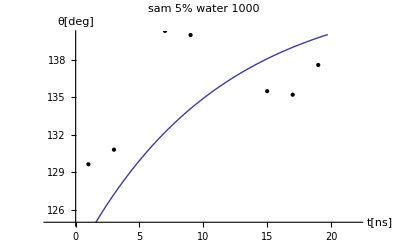

```mathematica
s5w1000={{1,129.633},{3,130.8},{5,102.754}, {7,140.292}, {9,139.963 }, {11,144.127}, {13,141.048},{15,135.476}, {17,135.191},{19,137.569}}
model=a+b Exp[-t/c ];
fit=FindFit[s5w1000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,-2,22},Epilog->Map[Point,s5w1000],PlotRange->{125,140},AxesLabel->{"t[ns]","θ[deg]"},PlotLabel->"sam 5% water 1000"]
```

{{1,155.},{3,137.697},{5,138.075},{7,136.829},{9,136.891},{11,136.677},{13,136.535},{15,135.672},{17,135.94},{19,136.594}}

{a→138.591}

Function[{t},138.591]

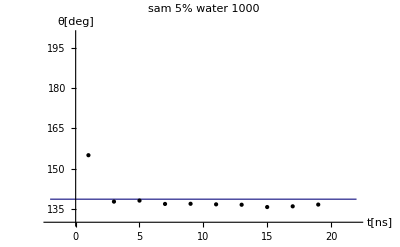

```mathematica
s5w2000={{1,155.},{3,137.697},{5,138.075},{7,136.829},{9,136.891},{11,136.677},{13,136.535},{15,135.672},{17,135.94},{19,136.594}}
model=a;
fit=FindFit[s5w2000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,-2,22},Epilog->Map[Point,s5w2000],PlotRange->{130,200},AxesLabel->{"t[ns]","θ[deg]"},PlotLabel->"sam 5% water 1000"]
```

{{1,159.527},{3,140.832},{5,137.755},{7,137.345},{9,135.455},{11,137.009},{13,137.225},{15,137.098},{17,138.235},{19,139.343}}

{a→137.365,b→56.6757,c→1.06536}

Function[{t},137.365+56.6757 ⅇ^(-0.938651 t)]

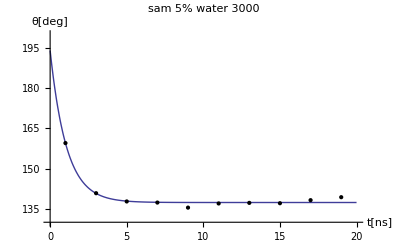

```mathematica
s5w3000= {{1,159.527},{3,140.832},{5,137.755},{7,137.345},{9,135.455},{11,137.009},{13,137.225},{15,137.098},{17,138.235},{19,139.343}}
model=a+b Exp[-t/c ];
fit=FindFit[s5w3000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s5w3000],PlotRange->{130,200},AxesLabel->{"t[ns]","θ[deg]"},PlotLabel->"sam 5% water 3000"]
```

{{1,164.237},{3,145.057},{5,138.74},{7,134.275},{9,133.364},{11,130.989},{13,130.635},{15,129.999},{17,129.734},{19,131.052}}

{a→130.451,b→48.5556,c→2.68115}

Function[{t},130.451+48.5556 ⅇ^(-0.372975 t)]

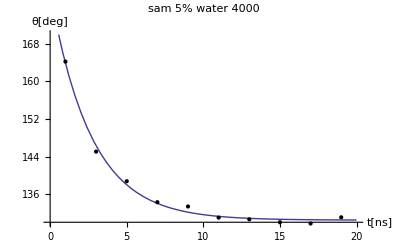

```mathematica
s5w4000={{1,164.237},{3,145.057},{5,138.74},{7,134.275},{9,133.364},{11,130.989},{13,130.635},{15,129.999},{17,129.734},{19,131.052}}
model=a+b Exp[-t/c];
fit=FindFit[s5w4000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s5w4000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{130,170},PlotLabel->"sam 5% water 4000"]
```

{{1,133.08},{3,116.974},{5,117.5},{7,114.25},{9,120.002},{11,113.742},{13,114.419},{15,112.379},{17,120.168},{19,114.274}}

{a→117.679}

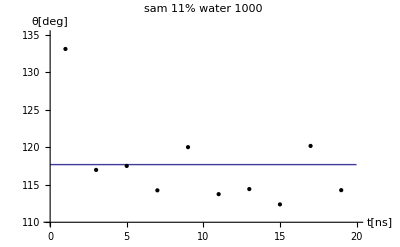

```mathematica
s11w1000={{1,133.08},{3,116.974},{5,117.5},{7,114.25},{9,120.002},{11,113.742},{13,114.419},{15,112.379},{17,120.168},{19,114.274}}
model=a;
fit=FindFit[s11w1000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s11w1000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{110,135},PlotLabel->"sam 11% water 1000"]
```

{{1,138.812},{3,113.174},{5,113.897},{7,116.849},{9,117.973},{11,117.846},{13,116.892},{15,116.766},{17,117.369},{19,116.368}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→116.348,Null→1.,b→5818.49,c→0.179948}

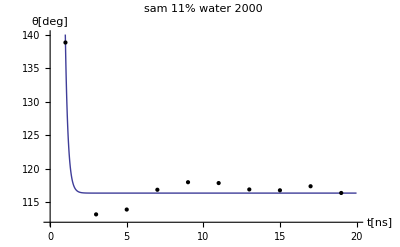

```mathematica
s11w2000={{1,138.812},{3,113.174},{5,113.897},{7,116.849},{9,117.973},{11,117.846},{13,116.892},{15,116.766},{17,117.369},{19,116.368}}
model=a+b Exp[-t/c];
fit=FindFit[s11w2000,model,{{a,116},,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s11w2000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{112,140},PlotLabel->"sam 11% water 2000"]
```

{{1,150.384},{3,119.204},{5,114.339},{7,115.113},{9,114.739},{11,115.183},{13,115.239},{15,113.432},{17,114.885},{19,114.772}}

{a→114.659,b→102.36,c→0.950256}

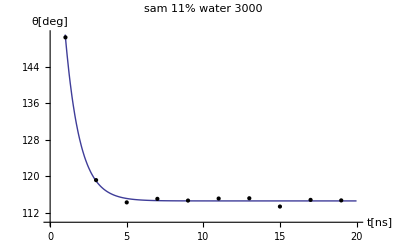

```mathematica
s11w3000={{1,150.384},{3,119.204},{5,114.339},{7,115.113},{9,114.739},{11,115.183},{13,115.239},{15,113.432},{17,114.885},{19,114.772}}
model=a+b Exp[-t/c];
fit=FindFit[s11w3000,model,{{a,115},b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s11w3000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{110,151},PlotLabel->"sam 11% water 3000"]
```

{{1,160.054},{3,127.994},{5,120.59},{7,119.115},{9,118.679},{11,117.765},{13,118.247},{15,116.603},{17,118.736},{19,118.922}}

{a→118.187,b→86.0202,c→1.38802}

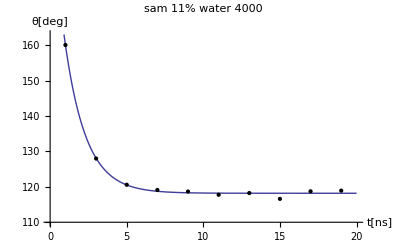

```mathematica
s11w4000={{1,160.054},{3,127.994},{5,120.59},{7,119.115},{9,118.679},{11,117.765},{13,118.247},{15,116.603},{17,118.736},{19,118.922}}
model=a+b Exp[-t/c];
fit=FindFit[s11w4000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s11w4000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{110,163},PlotLabel->"sam 11% water 4000"]
```

{{1,119.412},{3,107.767},{5,106.827},{7,106.794},{9,106.245},{11,109.555},{13,107.503},{15,108.614},{17,107.11},{19,113.559}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→108.219,b→1711.57,c→0.198802}

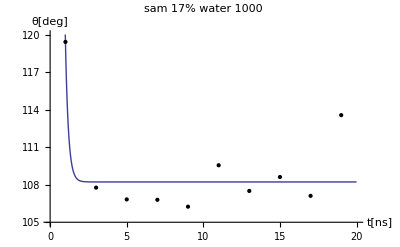

```mathematica
s17w1000={{1,119.412},{3,107.767},{5,106.827},{7,106.794},{9,106.245},{11,109.555},{13,107.503},{15,108.614},{17,107.11},{19,113.559}}
model=a+b Exp[-t/c];
fit=FindFit[s17w1000,model,{{a,108},b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s17w1000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{105,120},PlotLabel->"sam 17% water 1000"]
```

{{1,125.777},{3,102.067},{5,100.307},{7,99.0267},{9,98.7526},{11,99.6974},{13,100.681},{15,100.761},{17,100.533},{19,102.754}}

{a→103.036}

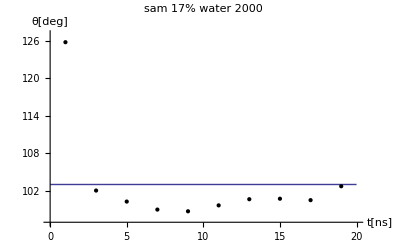

```mathematica
s17w2000={{1,125.777},{3,102.067},{5,100.307},{7,99.0267},{9,98.7526},{11,99.6974},{13,100.681},{15,100.761},{17,100.533},{19,102.754}}
model=a;
fit=FindFit[s17w2000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s17w2000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{97,127},PlotLabel->"sam 17% water 2000"]
```

{{1,146.217},{3,107.083},{5,103.169},{7,103.868},{9,102.784},{11,102.997},{13,104.557},{15,101.768},{17,102.51},{19,99.7134}}

{a→102.597,b→135.085,c→0.884573}

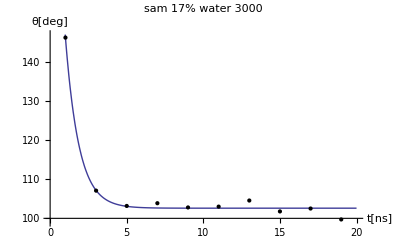

```mathematica
s17w3000={{1,146.217},{3,107.083},{5,103.169},{7,103.868},{9,102.784},{11,102.997},{13,104.557},{15,101.768},{17,102.51},{19,99.7134}}
model=a+b Exp[-t/c];
fit=FindFit[s17w3000,model,{{a,103},b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s17w3000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{99,147},PlotLabel->"sam 17% water 3000"]
```

{{1,156.262},{3,123.342},{5,103.917},{7,102.059},{9,100.882},{11,102.105},{13,102.234},{15,102.522},{17,102.343},{19,104.417}}

{a→101.775,b→95.7532,c→1.8087}

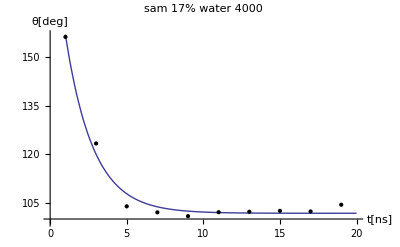

```mathematica
s17w4000={{1,156.262},{3,123.342},{5,103.917},{7,102.059},{9,100.882},{11,102.105},{13,102.234},{15,102.522},{17,102.343},{19,104.417}}
model=a+b Exp[-t/c];
fit=FindFit[s17w4000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s17w4000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{99,157},PlotLabel->"sam 17% water 4000"]
```

{{1,150.436},{3,143.958},{5,142.061},{7,143.985},{9,144.951},{11,143.335},{13,139.868},{15,144.474},{17,142.28},{19,141.694}}

{a→142.832,b→21.3108,c→0.971425}

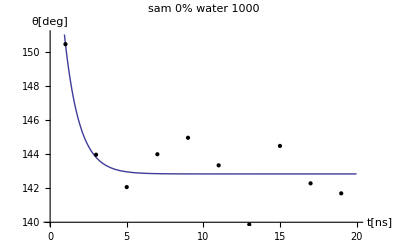

```mathematica
s0w1000={{1,150.436},{3,143.958},{5,142.061},{7,143.985},{9,144.951},{11,143.335},{13,139.868},{15,144.474},{17,142.28},{19,141.694}}
model=a+b Exp[-t/c];
fit=FindFit[s0w1000,model,{{a,140},b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s0w1000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{140,151},PlotLabel->"sam 0% water 1000"]
```

{{1,170.195},{3,138.119},{5,138.881},{7,137.974},{9,140.904},{11,139.369},{13,138.672},{15,138.031},{17,137.796},{19,138.295}}

{a→141.824}

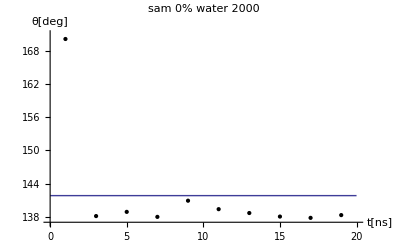

```mathematica
s0w2000={{1,170.195},{3,138.119},{5,138.881},{7,137.974},{9,140.904},{11,139.369},{13,138.672},{15,138.031},{17,137.796},{19,138.295}}
model=a;
fit=FindFit[s0w2000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s0w2000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{137,171},PlotLabel->"sam 0% water 2000"]
```

{{1,173.579},{3,148.416},{5,140.789},{7,139.919},{9,139.778},{11,139.95},{13,139.23},{15,138.903},{17,139.409},{19,141.355}}

{a→139.63,b→68.744,c→1.4208}

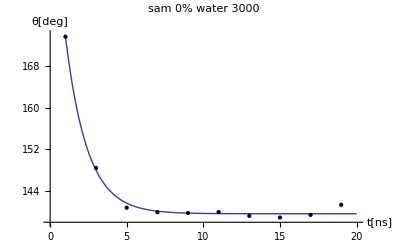

```mathematica
s0w3000={{1,173.579},{3,148.416},{5,140.789},{7,139.919},{9,139.778},{11,139.95},{13,139.23},{15,138.903},{17,139.409},{19,141.355}}
model=a+b Exp[-t/c];
fit=FindFit[s0w3000,model,{{a,138},b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s0w3000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{138,174},PlotLabel->"sam 0% water 3000"]
```

{{5,146.607},{7,142.131},{9,140.475},{11,139.271},{13,140.937},{15,138.767},{17,138.327},{19,138.457}}

{a→138.808,b→50.3067,c→2.66113}

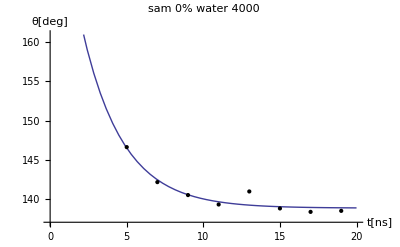

```mathematica
s0w4000={{5,146.607},{7,142.131},{9,140.475},{11,139.271},{13,140.937},{15,138.767},{17,138.327},{19,138.457}}
model=a+b Exp[-t/c];
fit=FindFit[s0w4000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,s0w4000],AxesLabel->{"t[ns]","θ[deg]"},PlotRange->{137,161},PlotLabel->"sam 0% water 4000"]
```

{{1,0.975234},{3,1.17441},{5,1.23197},{7,1.17233},{9,1.14339},{11,1.19293},{13,1.29191},{15,1.15696},{17,1.21579},{19,1.23445}}

{a→1.20475,b→-0.693258,c→0.905514}

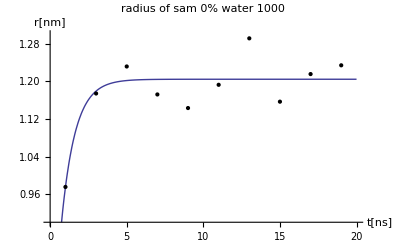

```mathematica
r0w1000={{1,0.975234},{3,1.17441},{5,1.23197},{7,1.17233},{9,1.14339},{11,1.19293},{13,1.29191},{15,1.15696},{17,1.21579},{19,1.23445}}
model=a+b Exp[-t/c];
fit=FindFit[r0w1000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r0w1000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{0.9,1.3},PlotLabel->"radius of sam 0% water 1000"]
```

{{3,1.66631},{5,1.63937},{7,1.67167},{9,1.57002},{11,1.628},{13,1.64557},{15,1.669},{17,1.67701},{19,1.66106}}

{a→1.64756}

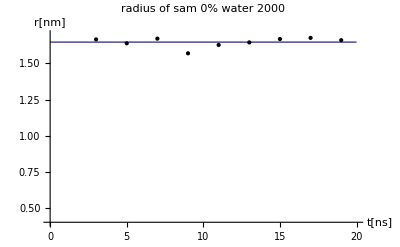

```mathematica
r02000={{3,1.66631},{5,1.63937},{7,1.67167},{9,1.57002},{11,1.628},{13,1.64557},{15,1.669},{17,1.67701},{19,1.66106}}
model=a;
fit=FindFit[r02000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r02000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{0.4,1.7},PlotLabel->"radius of sam 0% water 2000"]
```

{{1,0.307278},{3,1.46014},{5,1.78419},{7,1.82164},{9,1.82856},{11,1.81999},{13,1.85058},{15,1.86581},{17,1.84426},{19,1.76907}}

{a→1.83491,b→-3.16018,c→1.37811}

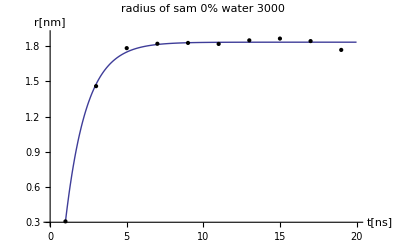

```mathematica
r03000={{1,0.307278},{3,1.46014},{5,1.78419},{7,1.82164},{9,1.82856},{11,1.81999},{13,1.85058},{15,1.86581},{17,1.84426},{19,1.76907}}
model=a+b Exp[-t/c];
fit=FindFit[r03000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r03000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{0.3,1.9},PlotLabel->"radius of sam 0% water 3000"]
```

{{5,1.69689},{7,1.90375},{9,1.98092},{11,2.03761},{13,1.96635},{15,2.06102},{17,2.08147},{19,2.07509}}

{a→2.06054,b→2.3048,c→2.68713}

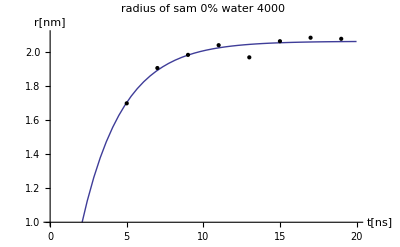

```mathematica
r04000={{5,1.69689},{7,1.90375},{9,1.98092},{11,2.03761},{13,1.96635},{15,2.06102},{17,2.08147},{19,2.07509}}
model=a-b Exp[-t/c];
fit=FindFit[r04000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r04000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.0,2.1},PlotLabel->"radius of sam 0% water 4000"]
```

{{1,1.5792},{3,1.55451},{5,2.86866},{7,1.31408},{9,1.31475},{11,1.19759},{13,1.28856},{15,1.44295},{17,1.44025},{19,1.37782}}

{a→1.53784}

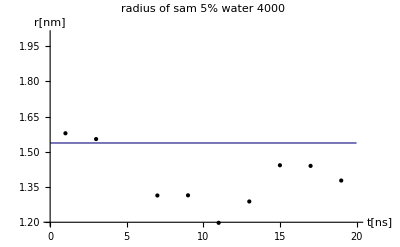

```mathematica
r51000={{1,1.5792},{3,1.55451},{5,2.86866},{7,1.31408},{9,1.31475},{11,1.19759},{13,1.28856},{15,1.44295},{17,1.44025},{19,1.37782}}
model=a;
fit=FindFit[r51000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r51000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.2,2.0},PlotLabel->"radius of sam 5% water 4000"]
```

{{1,1.04397},{3,1.69591},{5,1.6819},{7,1.71867},{9,1.71823},{11,1.72525},{13,1.73022},{15,1.76231},{17,1.75229},{19,1.72771}}

{a→1.72792,b→-2.94601,c→0.684693}

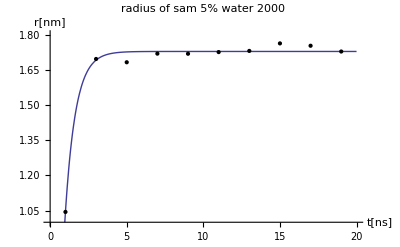

```mathematica
r52000={{1,1.04397},{3,1.69591},{5,1.6819},{7,1.71867},{9,1.71823},{11,1.72525},{13,1.73022},{15,1.76231},{17,1.75229},{19,1.72771}}
model=a+b Exp[-t/c];
fit=FindFit[r52000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r52000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.0,1.8},PlotLabel->"radius of sam 5% water 2000"]
```

{{3,1.78004},{5,1.90252},{7,1.91827},{9,1.99955},{11,1.93416},{13,1.92492},{15,1.93038},{17,1.89178},{19,1.84418}}

1.90287

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{a→1.}

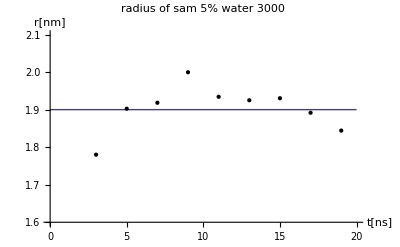

```mathematica
r53000={{3,1.78004},{5,1.90252},{7,1.91827},{9,1.99955},{11,1.93416},{13,1.92492},{15,1.93038},{17,1.89178},{19,1.84418}}
average=(1.78004+1.90252+1.91827+1.99955+1.93416+1.92492+1.93038+1.89178+1.84418)/9
fit=FindFit[r02000,model,{a},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r53000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.6,2.1},PlotLabel->"radius of sam 5% water 3000"]
```

{{1,0.828467},{3,1.76257},{5,2.05134},{7,2.24658},{9,2.28803},{11,2.39395},{13,2.41957},{15,2.44824},{17,2.45896},{19,2.40947}}

{a→2.42337,b→-2.32032,c→2.58693}

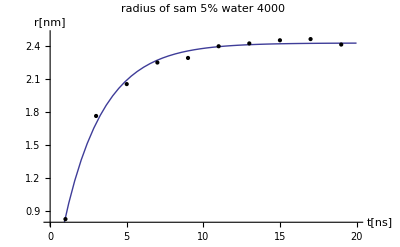

```mathematica
r54000={{1,0.828467},{3,1.76257},{5,2.05134},{7,2.24658},{9,2.28803},{11,2.39395},{13,2.41957},{15,2.44824},{17,2.45896},{19,2.40947}}
model=a+b Exp[-t/c];
fit=FindFit[r54000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r54000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{0.8,2.5},PlotLabel->"radius of sam 5% water 4000"]
```

{{1,1.51555},{3,1.91739},{5,1.90435},{7,1.99576},{9,1.86198},{11,2.02679},{13,2.00819},{15,2.0639},{17,1.90565},{19,2.04662}}

{a→1.98204,b→-1.05947,c→1.21142}

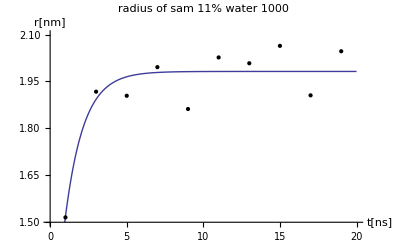

```mathematica
r111000={{1,1.51555},{3,1.91739},{5,1.90435},{7,1.99576},{9,1.86198},{11,2.02679},{13,2.00819},{15,2.0639},{17,1.90565},{19,2.04662}}
model=a+b Exp[-t/c];
fit=FindFit[r111000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r111000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.5,2.1},PlotLabel->"radius of sam 11% water 1000"]
```

{{1,1.65922},{3,2.51413},{5,2.4893},{7,2.40372},{9,2.34666},{11,2.35264},{13,2.3849},{15,2.38676},{17,2.36538},{19,2.38551}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→2.40322,b→-208.646,c→0.177412}

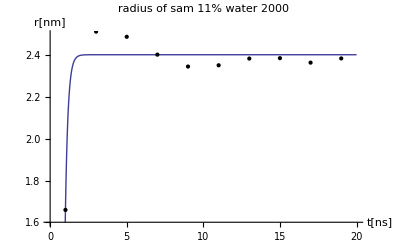

```mathematica
r112000={{1,1.65922},{3,2.51413},{5,2.4893},{7,2.40372},{9,2.34666},{11,2.35264},{13,2.3849},{15,2.38676},{17,2.36538},{19,2.38551}}
model=a+b Exp[-t/c];
fit=FindFit[r112000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r112000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.6,2.5},PlotLabel->"radius of sam 11% water 2000"]
```

{{1,1.37453},{3,2.61622},{5,2.79413},{7,2.78005},{9,2.79361},{11,2.77599},{13,2.77482},{15,2.82657},{17,2.7876},{19,2.79271}}

{a→2.79308,b→-4.07472,c→0.9479}

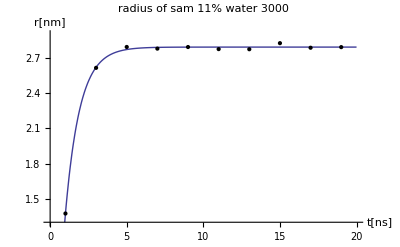

```mathematica
r113000={{1,1.37453},{3,2.61622},{5,2.79413},{7,2.78005},{9,2.79361},{11,2.77599},{13,2.77482},{15,2.82657},{17,2.7876},{19,2.79271}}
model=a+b Exp[-t/c];
fit=FindFit[r113000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r113000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.3,2.9},PlotLabel->"radius of sam 11% water 3000"]
```

{{1,1.0444},{3,2.51617},{5,2.82945},{7,2.87724},{9,2.90763},{11,2.94958},{13,2.92714},{15,2.98175},{17,2.90898},{19,2.8846}}

{a→2.92339,b→-4.00751,c→1.31957}

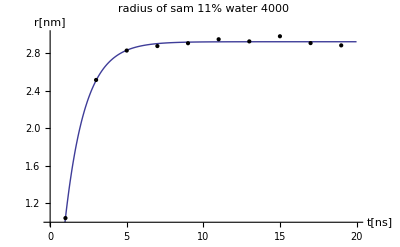

```mathematica
r114000={{1,1.0444},{3,2.51617},{5,2.82945},{7,2.87724},{9,2.90763},{11,2.94958},{13,2.92714},{15,2.98175},{17,2.90898},{19,2.8846}}
model=a+b Exp[-t/c];
fit=FindFit[r114000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r114000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.0,3.0},PlotLabel->"radius of sam 11% water 4000"]
```

{{1,1.92057},{3,2.18968},{5,2.19688},{7,2.19833},{9,2.21322},{11,2.14281},{13,2.20143},{15,2.14641},{17,2.18799},{19,2.06357}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→2.17115,b→-55.3579,c→0.185258}

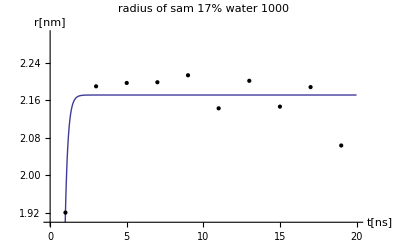

```mathematica
r171000={{1,1.92057},{3,2.18968},{5,2.19688},{7,2.19833},{9,2.21322},{11,2.14281},{13,2.20143},{15,2.14641},{17,2.18799},{19,2.06357}}
model=a+b Exp[-t/c];
fit=FindFit[r171000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r171000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.9,2.3},PlotLabel->"radius of sam 17% water 1000"]
```

{{1,2.10812},{3,2.84148},{5,2.87547},{7,2.91852},{9,2.92993},{11,2.89387},{13,2.91412},{15,2.93323},{17,2.9206},{19,2.86866}}

{a→2.90819,b→-2.68311,c→0.826261}

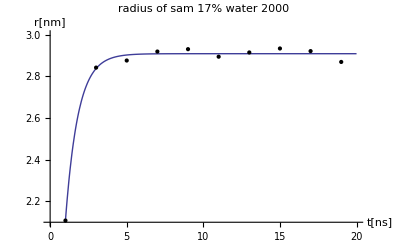

```mathematica
r172000={{1,2.10812},{3,2.84148},{5,2.87547},{7,2.91852},{9,2.92993},{11,2.89387},{13,2.91412},{15,2.93323},{17,2.9206},{19,2.86866}}
model=a+b Exp[-t/c];
fit=FindFit[r172000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r172000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{2.1,3.0},PlotLabel->"radius of sam 17% water 2000"]
```

{{1,1.55206},{3,3.01827},{5,3.22327},{7,3.16801},{9,3.18525},{11,3.18015},{13,3.14111},{15,3.2241},{17,3.17274},{19,3.30175}}

{a→3.20127,b→-5.05735,c→0.892604}

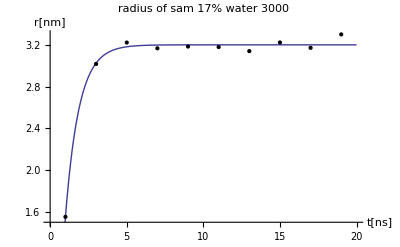

```mathematica
r173000={{1,1.55206},{3,3.01827},{5,3.22327},{7,3.16801},{9,3.18525},{11,3.18015},{13,3.14111},{15,3.2241},{17,3.17274},{19,3.30175}}
model=a+b Exp[-t/c];
fit=FindFit[r173000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r173000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.5,3.3},PlotLabel->"radius of sam 17% water 3000"]
```

{{1,1.22754},{3,2.72741},{5,3.44989},{7,3.55146},{9,3.59815},{11,3.54832},{13,3.5677},{15,3.55548},{17,3.56155},{19,3.4958}}

{a→3.57542,b→-4.1864,c→1.74995}

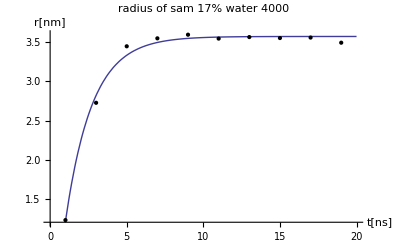

```mathematica
r174000={{1,1.22754},{3,2.72741},{5,3.44989},{7,3.55146},{9,3.59815},{11,3.54832},{13,3.5677},{15,3.55548},{17,3.56155},{19,3.4958}}
model=a+b Exp[-t/c];
fit=FindFit[r174000,model,{a,b,c},t]
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,20},Epilog->Map[Point,r174000],AxesLabel->{"t[ns]","r[nm]"},PlotRange->{1.2,3.6},PlotLabel->"radius of sam 17% water 4000"]
```

```mathematica
Results 0pc
```

{{1.20475,142.832},{1.66631,141.824},{1.83491,139.63},{2.06054,138.808}}

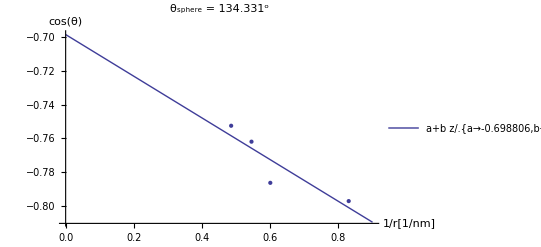

a+b z

```mathematica
AngleRad0pc={{1.20475,142.832},{1.66631,141.824},{1.83491,139.63},{2.06054,138.808}}
CAR=Table[{1/AngleRad0pc[[i,1]],Cos[AngleRad0pc[[i,2]]/180 Pi]},{i,1,4}];
fkt=a+b z;fit1=FindFit[CAR,fkt,{a,b},z];
Show[Plot[{fkt/.fit1},{z,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{CAR}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[a/.fit1]180/Pi]<>"^o"]
fkt
```

```mathematica
lm2=LinearModelFit[CAR,x,x]
 lm2["ParameterTable"]
```

FittedModel[-0.698806-0.122799 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.698806 | 0.0269181 | -25.9604 | 0.00148051
x | -0.122799 | 0.0428072 | -2.86865 | 0.103072

```mathematica
Results 5pc
```

{{1.53784,143.623},{1.72792,138.591},{1.90287,137.365},{2.42337,130.451}}

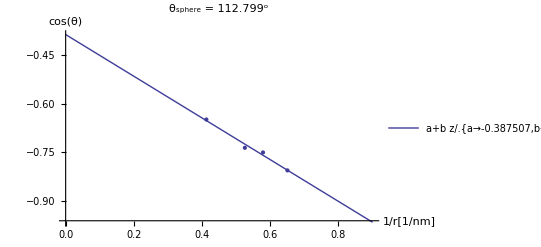

```mathematica
AngleRad5pc={{1.53784,143.623},{1.72792,138.591},{1.90287,137.365},{2.42337,130.451}}
CAR=Table[{1/AngleRad5pc[[i,1]],Cos[AngleRad5pc[[i,2]]/180 Pi]},{i,1,4}];
fkt=a+b z;fit1=FindFit[CAR,fkt,{a,b},z];
Show[Plot[{fkt/.fit1},{z,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{CAR}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[a/.fit1]180/Pi]<>"^o"]
```

```mathematica
lm=LinearModelFit[CAR,x,x]
```

FittedModel[-0.387507-0.641203 x]

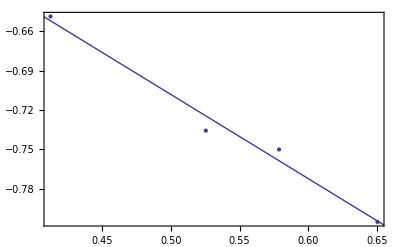

```mathematica
Show[ListPlot[CAR],Plot[lm[x],{x,0,1}],Frame->True]
```

```mathematica
lm["FitResiduals"]
```

{-0.000674444,0.00858363,-0.0112101,0.00330097}

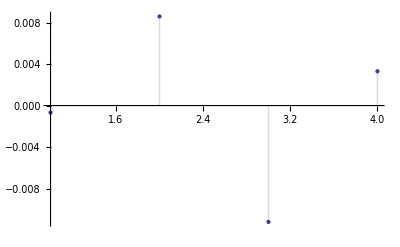

```mathematica
ListPlot[lm["FitResiduals"],Filling->Axis]
```

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.387507 | 0.032475 | -11.9325 | 0.00695013
x | -0.641203 | 0.0591869 | -10.8335 | 0.00841301

```mathematica
lm["MeanPredictionConfidenceIntervalTable"]
```

Observed | Predicted | Standard Error | Confidence Interval
-0.805132 | -0.804458 | 0.00821918 | {-0.839822,-0.769093}
-0.750007 | -0.758591 | 0.00557828 | {-0.782592,-0.734589}
-0.735683 | -0.724473 | 0.00522153 | {-0.74694,-0.702007}
-0.648798 | -0.652098 | 0.00920656 | {-0.691711,-0.612486}

```mathematica
e=lm["SinglePredictionErrors"]
```

{0.0131493,0.0116819,0.0115158,0.013788}

```mathematica
CAR
```

{{0.650263,-0.805132},{0.57873,-0.750007},{0.525522,-0.735683},{0.412649,-0.648798}}

```mathematica
CAR[[4,2]]
```

-0.648798

```mathematica
ErrorListPlot[{{{0.6502627061332779,-0.8051319461067109},ErrorBar[0.01314927939834847]},{{0.5787304967822585,-0.7500071817518709},ErrorBar[0.011681860842326124]},{{0.5255219747013721,-0.7356834698053561},ErrorBar[0.011515771421411867]},{{0.41264850187961394,-0.648797503110901},ErrorBar[0.01378801749526198]}}]
```

ErrorListPlot[{{{0.650263,-0.805132},ErrorBar[0.0131493]},{{0.57873,-0.750007},ErrorBar[0.0116819]},{{0.525522,-0.735683},ErrorBar[0.0115158]},{{0.412649,-0.648798},ErrorBar[0.013788]}}]

```mathematica
m=(4*Sum[CAR[[i,1]]*CAR[[i,2]],{i,4}]-Sum[CAR[[i,1]],{i,4}]*Sum[CAR[[i,2]],{i,4}])/(4*Sum[CAR[[i,1]]^2,{i,4}]-Sum[CAR[[i,1]],{i,4}]^2)
b=(Sum[CAR[[i,1]]^2,{i,4}]*Sum[CAR[[i,2]],{i,4}]-Sum[CAR[[i,1]],{i,4}]*Sum[CAR[[i,1]]*CAR[[i,2]],{i,4}])/(4*Sum[CAR[[i,1]]^2,{i,4}]-Sum[CAR[[i,1]],{i,4}]^2)
```

-0.641203

-0.387507

```mathematica
Δ=4*Sum[CAR[[i,1]]^2,{i,4}]-Sum[CAR[[i,1]],{i,4}]^2
```

0.120292

```mathematica
σy=Sqrt[0.5*Sum[(CAR[[i,2]]-b-m*CAR[[i,1]])^2,{i,4}]]
σb=Sqrt[Sum[CAR[[i,1]]^2,{i,4}]/Δ*σy^2]
σm=Sqrt[4/Δ*σy^2]
```

0.0102639

0.032475

0.0591869

```mathematica
Results 11pc
```

{{1.98204,117.679},{2.40322,116.348},{2.79308,114.659}}

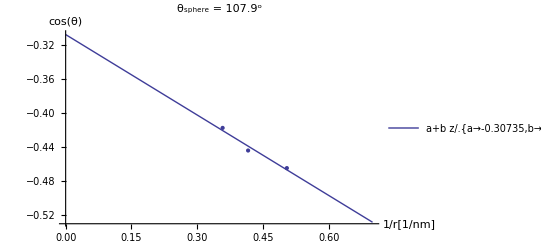

```mathematica
AngleRad11pc={{1.98204,117.679},{2.40322,116.348},{2.79308,114.659}}
CAR=Table[{1/AngleRad11pc[[i,1]],Cos[AngleRad11pc[[i,2]]/180 Pi]},{i,1,3}];
fkt=a+b z;fit1=FindFit[CAR,fkt,{a,b},z];

Show[Plot[{fkt/.fit1},{z,0,0.7},PlotLegends->LineLegend["Expressions"]],ListPlot[{CAR}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[a/.fit1]180/Pi]<>"^o"]
```

```mathematica
{{1.98204,117.679},{2.40322,116.348},{2.79308,114.659}}
```

{{1.98204,117.679},{2.40322,116.348},{2.79308,114.659}}

```mathematica
lm3=LinearModelFit[CAR,x,x]
 lm3["ParameterTable"]
```

FittedModel[-0.30735-0.315568 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.30735 | 0.0262678 | -11.7006 | 0.0542772
x | -0.315568 | 0.0610231 | -5.17129 | 0.121606

```mathematica
Results 17pc
```

{{2.17115,108.219},{2.90819,103.036},{3.20127,102.597},{3.57542,101.775}}

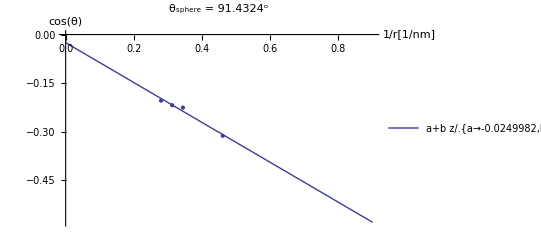

```mathematica
AngleRad17pc={{2.17115,108.219},{2.90819,103.036},{3.20127,102.597},{3.57542,101.775}}
CAR=Table[{1/AngleRad17pc[[i,1]],Cos[AngleRad17pc[[i,2]]/180 Pi]},{i,1,4}];
fkt=a+b z;fit1=FindFit[CAR,fkt,{a,b},z];

Show[Plot[{fkt/.fit1},{z,0,0.9},PlotLegends->LineLegend["Expressions"]],ListPlot[{CAR}],AxesLabel->{"1/r[1/nm]","cos(θ)"},PlotLabel->"θ_sphere = "<>ToString[ArcCos[a/.fit1]180/Pi]<>"^o"]
```

```mathematica
lm4=LinearModelFit[CAR,x,x]
 lm4["ParameterTable"]
```

FittedModel[-0.0249982-0.616096 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0249982 | 0.0253058 | -0.987844 | 0.427357
x | -0.616096 | 0.0711373 | -8.66066 | 0.0130712

```mathematica
General Results Of All Contact Angles
```

{{0,134.3 All Angles Contact General Of},{5 All Angles Contact General Of,112.8 All Angles Contact General Of},{11 All Angles Contact General Of,107.9 All Angles Contact General Of},{17 All Angles Contact General Of,91.4 All Angles Contact General Of},{66 All Angles Contact General Of,0}}

{{0,134.3},{5,112.8},{11,107.9},{17,91.4},{66,0}}

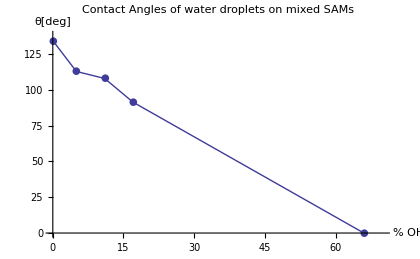

```mathematica
Results={{0,134.3},{5,112.8},{11,107.9},{17,91.4},{66,0}}
Show[ListLinePlot[Results],ListPlot[Results,PlotMarkers->{●,10}],PlotRange->{{0,70},{0,138}},AxesLabel->{"% OH","θ[deg]"},PlotLabel->"Contact Angles of water droplets on mixed SAMs"]
```

```mathematica
Slope Results
```

{{0,-0.122799},{5,-0.641203},{11,-0.315568},{17,-0.616096},{66,0}}

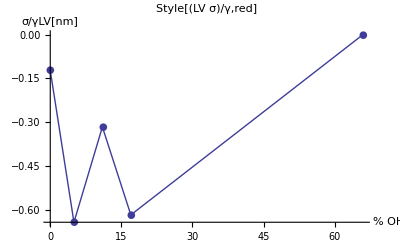

```mathematica
slopeResults={{0,-0.1227990653146828},{5,-0.6412033926430145},{11,-0.3155680548757708},{17,-0.6160961300394217},{66,0}}
Show[ListLinePlot[slopeResults],ListPlot[slopeResults,PlotMarkers->{●,10}],PlotRange->{{0,70},{0,-0.7}},AxesLabel->{"% OH","σ/γLV[nm]"},PlotLabel->Style[Slopes=σ/γLV ,red]]
```

{-0.122799,-0.641203,-0.315568,-0.616096,0}

{-0.122799,-0.641203,-0.315568,-0.616096,0}

{6.47151,33.7914,16.6304,32.4683,0.}

{0,5,11,17,66}

{{6.47151,0},{33.7914,5},{16.6304,11},{32.4683,17},{0.,66}}

{{0,6.47151},{5,33.7914},{11,16.6304},{17,32.4683},{66,0.}}

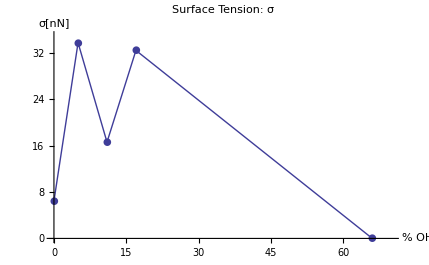

```mathematica
lineTension={-0.1227990653146828,-0.6412033926430145,-0.3155680548757708,-0.6160961300394217,0}
slope=lineTension
σ2=slope*(-52.7)
OH={0,5,11,17,66}
Transpose[{σ2, OH}]
sdata=Thread[{OH,σ2}]
Show[ListLinePlot[sdata],ListPlot[sdata,PlotMarkers->{●,10}],PlotRange->{{0,70},{0,35}},AxesLabel->{"% OH","σ[nN]"},PlotLabel->"Surface Tension: σ"]
```

### Errors

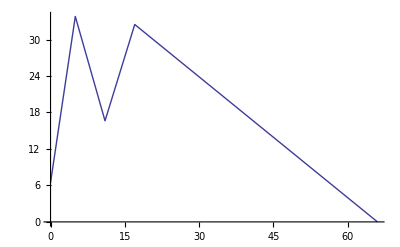

```mathematica
Needs["ErrorBarPlots`"]
ErrorListPlot[{{{0, 6.471510742083784},ErrorBar[0.026918130584387672]},{ {5, 33.79141879228687},ErrorBar[0.03247496955921518]},{ {11, 16.63043649195312},ErrorBar[0.02626783590614369]},{ {17, 32.46826605307752},ErrorBar[0.025305789579519972]},{{66,0.0},ErrorBar[0.0]}},Joined->True]
```

```mathematica
Results from Averages of the last 5 nm
```

```mathematica
x5 = {0.68619489, 0.54119603, 0.50237748, 0.39581126}
x11={0.48502561, 0.41137479, 0.35349246, 0.34113893}
x17={0.46118297, 0.33920858, 0.30539007, 0.27915884}
y5={-0.97296668, -0.02428263, -0.78254311, -0.92261447}
y11={0.99400102, -0.6288717,  0.92249037, -0.41023231}
y17={0.43560808, 0.61112816, 0.97984991, 0.18924371}
Transpose[{x5, y5}]
Transpose[{x11, y11}]
Transpose[{x17, y17}]
xy5=Thread[{x5,y5}]
xy11=Thread[{x11,y11}]
xy17=Thread[{x17,y17}]
fkt=a+b z;
fit5=FindFit[xy5,fkt,{a,b},z];
fit11=FindFit[xy11,fkt,{a,b},z];
fit17=FindFit[xy17,fkt,{a,b},z];
```

{0.686195,0.541196,0.502377,0.395811}

{0.485026,0.411375,0.353492,0.341139}

{0.461183,0.339209,0.30539,0.279159}

{-0.972967,-0.0242826,-0.782543,-0.922614}

{0.994001,-0.628872,0.92249,-0.410232}

{0.435608,0.611128,0.97985,0.189244}

{{0.686195,-0.972967},{0.541196,-0.0242826},{0.502377,-0.782543},{0.395811,-0.922614}}

{{0.485026,0.994001},{0.411375,-0.628872},{0.353492,0.92249},{0.341139,-0.410232}}

{{0.461183,0.435608},{0.339209,0.611128},{0.30539,0.97985},{0.279159,0.189244}}

{{0.686195,-0.972967},{0.541196,-0.0242826},{0.502377,-0.782543},{0.395811,-0.922614}}

{{0.485026,0.994001},{0.411375,-0.628872},{0.353492,0.92249},{0.341139,-0.410232}}

{{0.461183,0.435608},{0.339209,0.611128},{0.30539,0.97985},{0.279159,0.189244}}

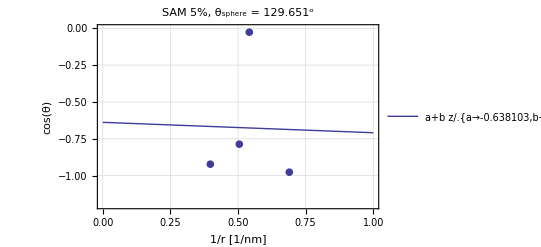

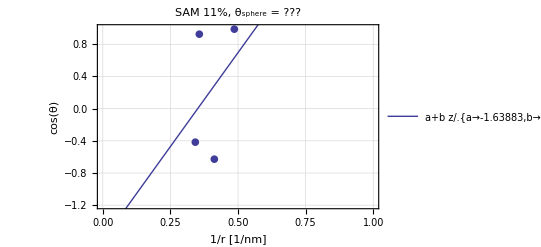

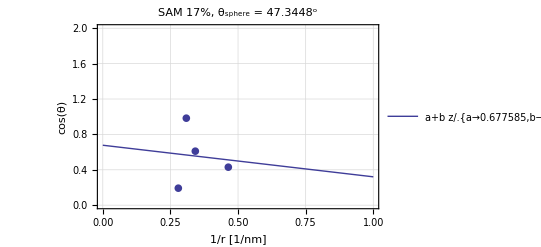

```mathematica
Show[Plot[{fkt/.fit5},{z,0,1},PlotLegends->LineLegend["Expressions"]],ListPlot[xy5,PlotMarkers->{●,10}],PlotRange->{{0,1},{-1.2,0}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, FrameLabel->{"1/r [1/nm]","cos(θ)"},PlotLabel->"SAM 5%, θ_sphere = "<>ToString[ArcCos[a/.fit5]180/Pi]<>"^o"]
Show[Plot[{fkt/.fit11},{z,0,1},PlotLegends->LineLegend["Expressions"]],ListPlot[xy11,PlotMarkers->{●,10}],PlotRange->{{0,1},{-1.2,1}},GridLines->Automatic,Frame->True,FrameTicks->Automatic,FrameLabel->{"1/r [1/nm]","cos(θ)"},PlotLabel->"SAM 11%, θ_sphere = ???"]
Show[Plot[{fkt/.fit17},{z,0,1},PlotLegends->LineLegend["Expressions"]],ListPlot[xy17,PlotMarkers->{●,10}],PlotRange->{{0,1},{0,2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic,FrameLabel->{"1/r [1/nm]","cos(θ)"},PlotLabel->"SAM 17%, θ_sphere = "<>ToString[ArcCos[a/.fit17]180/Pi]<>"^o"]
```

```mathematica
GridLines->{{0.05,0.1,0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.45, 0.5, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8, 0.85, 0.9, 0.95, 1,Dotted},{Automatic,Dotted}]
```

```mathematica
a/.fit11
```

-1.63883

```mathematica
ArcCos[-1.6388319787915586]
```

3.14159-1.07746 ⅈ